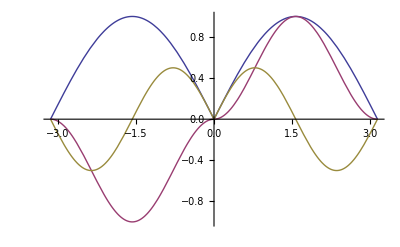

```mathematica
Plot[{Abs[Sin[x]], Sin[x]Abs[Sin[x]], Cos[x]Abs[Sin[x]]}, {x, -Pi, Pi}]
```

```mathematica
2/Pi Integrate[Abs[Sin[x]]Sin[n x],{x, -Pi, Pi}]
```

0

```mathematica
1/Pi Integrate[Abs[Sin[x]]Cos[n x],{x, -Pi, Pi}]
```

-(2 (1+Cos[n π]))/((-1+n^2) π)

```mathematica
2((-Cos[n Pi])/n^2+1/(n^2))/(1+1/(n^2))
```

(2 (1/n^2-Cos[n π]/n^2))/(1+1/n^2)

```mathematica
Simplify[%]
```

(2-2 Cos[n π])/(1+n^2)